# Continuous-time matching-alleles coevolution

Here we explore coevolution between a host and free-living pathogen.  By assuming host and parasite population sizes remain constant over time we are able to focus solely on the effects of coevolution (change in allele frequencies).  Using a Moran model design every host (pathogen) birth is coupled with a host (pathogen) death.  A schematic diagram showing the host-pathogen life cycle is given by figure 2 of the main text.

By running the following line and then compiling this Mathematica notebook will generate the plots found in the main text.

```mathematica
(*CreateDirectory[NotebookDirectory[]<>"Plots"]*)
```

```mathematica
PlotOptions={ImageSize->{Automatic,300},Frame->True,FrameTicks->{{True,False},{True,False}},FrameTicksStyle->Directive[Black,14],Background->White};
```

## Deterministic Model

Here we model the dynamics of host and pathogen in the deterministic limit, assuming that host and pathogen population population sizes are infinite.

Differential Equations

We model host-parasite coevolution in a symmetric matching-alleles model as given by the substitution list βSub. 
Although, it is most straightforward to derive the differential equations in terms the number of hosts of type i, nH[i,t], and the number of pathogens of type j, nP[j,t], we transform into the host and pathogen allele frequencies using the substitution pSub.

```mathematica
βSub={β[1,1]->X/κ,β[1,2]->Y/κ,β[2,1]->Y/κ,β[2,2]->X/κ};
pSub[t_]:={nH[1,t]->κ pH[t],nH[2,t]->κ (1-pH[t]),nP[1,t]->κ pP[t],nP[2,t]->κ (1-pP[t])};
Denom[t_]:=(Sum[β[i,j]α nH[i,t]nP[j,t],{j,1,2},{i,1,2}]+Sum[δ nH[i,t],{i,1,2}])/κ;
```

Differential equation for host allele frequency d/dt p_H(t)=gH(t)

```mathematica
gH[t_]:=1/κ(Sum[(β[i,j]α nH[i,t]nP[j,t])/Denom[t] ((-Mod[i,2])+nH[1,t]/κ),{j,1,2},{i,1,2}]+Sum[(δ nH[i,t])/Denom[t]((-Mod[i,2])+nH[1,t]/κ),{i,1,2}])/.βSub/.pSub[t]//FullSimplify
```

```mathematica
gH[t]//FullSimplify
```

((X-Y) α (-1+pH[t]) pH[t] (-1+2 pP[t]))/(X α+δ+(X-Y) α (-pP[t]+pH[t] (-1+2 pP[t])))

Differential equation for pathogen allele frequency d/dt p_H(t)=gH(t)

```mathematica
gP[t_]:=1/κ(Sum[β[i,j]α nH[i,t]nP[j,t]((Mod[j,2] M)-M nP[1,t]/κ),{j,1,2},{i,1,2}]/Denom[t]+Sum[(γ nP[j,t])/Denom[t] (Mod[j,2]M-M nP[1,t]/κ),{j,1,2}])/.M->1/.βSub/.pSub[t]//FullSimplify
```

```mathematica
gP[t]
```

-((X-Y) α (-1+2 pH[t]) (-1+pP[t]) pP[t])/(X α+δ+(X-Y) α (-pP[t]+pH[t] (-1+2 pP[t])))

Equilibria

```mathematica
equi=Solve[{gH[t]==0,gP[t]==0},{pH[t],pP[t]}]
```

{{pH[t]→0,pP[t]→0},{pH[t]→1,pP[t]→0},{pH[t]→1/2,pP[t]→1/2},{pH[t]→0,pP[t]→1},{pH[t]→1,pP[t]→1}}

Stability of the polymorphic equilibrium

```mathematica
jMtrxMoran = {{D[gH[t], pH[t]], D[gH[t], pP[t]]}, {D[gP[t], pH[t]], D[gP[t], pP[t]]}};
```

```mathematica
Eigenvalues[jMtrxMoran/.equi[[3]]]//FullSimplify
```

{(ⅈ (X-Y) α)/((X+Y) α+2 δ),-(ⅈ (X-Y) α)/((X+Y) α+2 δ)}

These eigenvalues are purely imaginary (0 real part) and hence the endemic equilibrium is characterized by neutrally stable cycles.  Not that it is straightforward to show that the remaining four equilibria are all unstable.

Numerical Integration

Numerical integration of host and pathogen allele frequency dynamics.

```mathematica
Clear[nsolMoran,pHsol,pPsol]
nsolMoran[pars_,inits_]:=nsolMoran[pars,inits]=NDSolve[{D[pH[t2],t2]==gH[t2]/.pars,D[pP[t2],t2]==gP[t2]/.pars,pH[0]==pH0/.inits,pP[0]==pP0/.inits},{pH[t2],pP[t2]},{t2,0,tMax/.pars}]//Flatten
(*Solution for allele frequencies*)
pHsol[τ_,pars_,inits_]:=pH[t2]/.nsolMoran[pars,inits]/.{t2->τ}
pPsol[τ_,pars_,inits_]:=pP[t2]/.nsolMoran[pars,inits]/.{t2->τ}
```

Test parameters and initial conditions

```mathematica
TestPars={X->0.8,Y->0.4,κ->100,δ->1,α->0.2,γ->1,(*M->3,*)tMax->250};
TestParsLong={X->0.8,Y->0.4,κ->100,δ->1,α->0.2,γ->1,(*M->3,*)tMax->1000};
TestInits0={pH0->0.55,pP0->0.45};
TestInits={pH0->0.85,pP0->0.15};
TestInits2={pH0->0.7,pP0->0.3};
```

```mathematica
pHsol[0.5,TestPars,TestInits0]
```

0.550876

Allele frequency dynamics.  Host=Black Pathogen=Red.

```mathematica
tMax/.TestPars
```

350

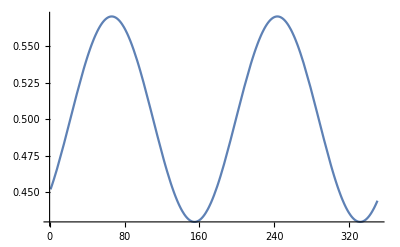

```mathematica
Plot[pPsol[t,TestPars,TestInits0],{t,1,tMax/.TestPars}]
```

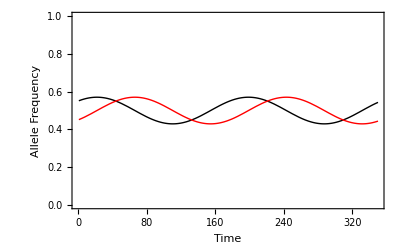

```mathematica
Show[Plot[{pHsol[t,TestPars,TestInits0],pPsol[t,TestPars,TestInits0]},{t,1,tMax/.TestPars},PlotStyle->{{Black,Thick},{Red,Thick}},PlotRange->{0,1},AxesLabel->{"Time","Allele Frequency"}],PlotOptions]
```

Phase plane of allele frequency dynamics.

```mathematica
DetDynAF[pars_,inits_,color_]:=Show[ListLinePlot[Table[{pHsol[τ,pars,inits],pPsol[τ,pars,inits]},{τ,0,tMax/.pars}],PlotRange->{{0,1},{0,1}},AspectRatio->1,PlotStyle->color]/.Line[x_]:>{Arrowheads[Table[.05,{r,{2}}]],
[x]},ListPlot[{{pH0,pP0}/.inits},PlotStyle->Red,PlotMarkers->{●,10}],PlotOptions]
```

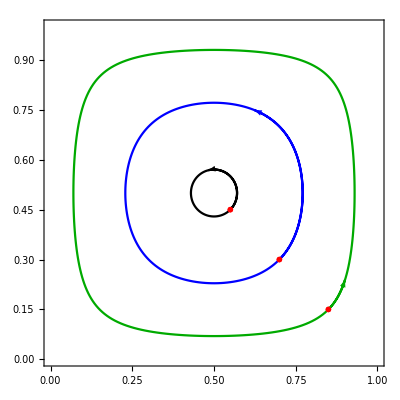

```mathematica
Show[DetDynAF[TestPars,TestInits0,Black],DetDynAF[TestPars,TestInits2,Blue],DetDynAF[TestPars,TestInits,Darker[Green]]]
Export[NotebookDirectory[]<>"Plots/Moran_Det_AF.pdf",%,ImageResolution->300];
```

Plot of heterozygosity as a function of time.

```mathematica
AvgH[pars_,inits_]:=Block[{temp},
temp=Table[2pHsol[τ,pars,inits](1-pHsol[τ,pars,inits]),{τ,0,tMax/.pars}];
Table[Mean[temp[[1;;x]]],{x,1,tMax+1/.pars}]
]
```

```mathematica
DetDynHet[pars_,inits_,color_]:=Show[
(*Heterozygosity Dynamics*)
ListLinePlot[Table[2pHsol[τ,pars,inits](1-pHsol[τ,pars,inits]),{τ,0,tMax/.pars}],PlotRange->{0,0.5},PlotStyle->color],
(*Initial conditions*)
ListPlot[{{0,2pH0(1-pH0)}/.inits},PlotStyle->Red,PlotMarkers->{●,10}],
(*Average Dynamics*)
ListLinePlot[AvgH[pars,inits],PlotRange->{0,0.5},PlotStyle->Directive[color,Dashed]],
(*PlotOptions*)
PlotOptions,AspectRatio->0.75]
```

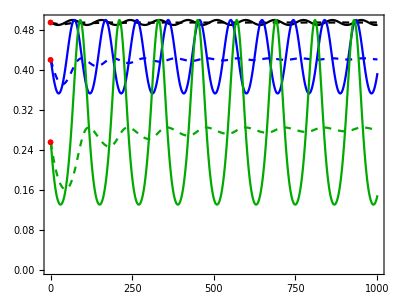

```mathematica
Show[DetDynHet[TestParsLong,TestInits0,Black],DetDynHet[TestParsLong,TestInits2,Blue],DetDynHet[TestParsLong,TestInits,Darker[Green]],Background->White]
Export[NotebookDirectory[]<>"Plots/Moran_Det_Het.pdf",%,ImageResolution->300];
```

Neutral Expectation

For the neutral Moran model, heterozygosity after k events 1/2(1-2/κ^2)^k  given the initial heterozygosity of H_0=1/2.  Probability of k events by time ((κ t)^k Exp[-κ t])/(k!)

```mathematica
Clear[neutExp]
neutExp[κ_,t_]:=If[t==0,1/2,Sum[((κ t)^k Exp[-κ t])/(k!)1/2(1-2/κ^2)^k,{k,0,∞}]]
```

This simplifies to:

```mathematica
Sum[((κ t)^k Exp[-κ t])/(k!)1/2(1-2/κ^2)^k,{k,0,∞}]
```

1/2 ⅇ^(-(2 t)/κ)

```mathematica
neutExp[κ_,t_]:=1/2 ⅇ^(-(2 t)/κ)
```

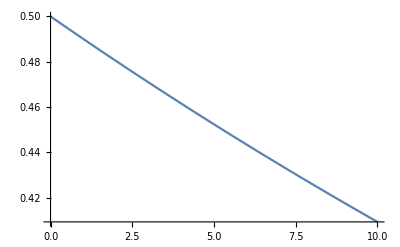

```mathematica
Plot[neutExp[100,t],{t,0,10}]
```

## Ensemble Moments

Substitutions

Let δX be the deviation of variable X from its value at the deterministic equilibrium.  
Let μδX be the expectation of deviation of X from equilibrium over all realizations of the stochastic process.
Let CδXY, CδXYZ,...  be the correlation, skew and higher order centralized moments of the variables X,Y,Z,...

### Moment Substitutions

Substitution lists that allows us to take the expectation of by substituting higher order moments in terms of lower order moments and the corresponding centralized moment.

```mathematica
first={δH->μδH,δP->μδP};
```

```mathematica
second=Block[{out},out={};
AppendTo[out,Solve[CδHH==Expand[(δH-μδH)^2]/.δH^2->X,X][[1]]/.first/.X->δH^2];
AppendTo[out,Solve[CδHP==Expand[(δH-μδH)(δP-μδP)]/.δH δP->X,X][[1]]/.first/.X->δH δP];
AppendTo[out,Solve[CδPP==Expand[(δP-μδP)^2]/.δP^2->X,X][[1]]/.first/.X->δP^2];
Flatten[out]
];
```

```mathematica
third=Block[{out},out={};
AppendTo[out,Solve[CδHHH==Expand[(δH-μδH)^3]/.δH^3->X,X][[1]]/.second/.first/.X->δH^3];
AppendTo[out,Solve[CδHHP==Expand[(δH-μδH)^2(δP-μδP)]/.δH^2 δP->X,X][[1]]/.second/.first/.X->δH^2 δP];
AppendTo[out,Solve[CδHPP==Expand[(δH-μδH)(δP-μδP)^2]/.δH δP^2->X,X][[1]]/.second/.first/.X->δH δP^2];
AppendTo[out,Solve[CδPP==Expand[(δP-μδP)^3]/.δP^3->X,X][[1]]/.second/.first/.X->δP^3];
Flatten[out]
];
```

```mathematica
fourth=Block[{out},out={};
AppendTo[out,Solve[CδHHHH==Expand[(δH-μδH)^4]/.δH^4->X,X][[1]]/.third/.second/.first/.X->δH^4];
AppendTo[out,Solve[CδHHHP==Expand[(δH-μδH)^3(δP-μδP)]/.δH^3 δP->X,X][[1]]/.third/.second/.first/.X->δH^3 δP];
AppendTo[out,Solve[CδHHPP==Expand[(δH-μδH)^2(δP-μδP)^2]/.δH^2 δP^2->X,X][[1]]/.third/.second/.first/.X->δH^2 δP^2];
AppendTo[out,Solve[CδHPPP==Expand[(δH-μδH)(δP-μδP)^3]/.δH δP^3->X,X][[1]]/.third/.second/.first/.X->δH δP^3];
AppendTo[out,Solve[CδPPPP==Expand[(δP-μδP)^4]/.δP^4->X,X][[1]]/.third/.second/.first/.X->δP^4];
Flatten[out]
];
```

### Simplification

Substitution of notation for the counts.

```mathematica
nSub={nH[1]->H,nH[2]->κ-H,nP[1]->P,nP[2]->κ-P};
```

Substituting counts into (and back from) deviations from the equilibrium.

Let δH=H-Ĥ and δP=P-P̂.  We will assume that the deviations from equilibrium, δH and δP, are small.

Note that the covariance between the deviations from equilibrium are equal to the the covariance in the original variables.

```mathematica
eSub={H->κ/2+ϵ δH,P->κ/2+ϵ δP};
```

```mathematica
μeSubRev={μδH->μH[τ]-κ/2,μδP->μP[τ]-κ/2,CδHH-> CHH[τ],CδHP->CHP[τ],CδPP->CPP[τ],CδHHH->CHHH[τ],CδHHP->CHHP[τ],CδHPP-> CHPP[τ],CδPPP->CPPP[τ]};
```

### Moment Closure

```mathematica
assump3={CδHHHH->0,CδHHHP->0,CδHHPP->0,CδHPPP->0,CδPPPP->0};
```

Rates f[x] and change in x

```mathematica
d[H_,P_]:=(Sum[α β[h,p]nH[h]nP[p],{h,1,2},{p,1,2}]+Sum[δ nH[h],{h,1,2}])/κ/.nSub/.βSub//FullSimplify
```

```mathematica
f[H_,P_]:=Join[(*Host Free-living death*)Flatten[Table[(δ nH[h1])/d[H,P] nH[h2]/κ/.nSub,{h1,1,2},{h2,1,2}]],(*Infectious Death of h1 by p1, h2 born,p2 born*)Flatten[Table[(α β[h1,p1])/d[H,P] nH[h1]nP[p1] nH[h2]/κ nP[p2]/κ/.nSub/.βSub,{h1,1,2},{p1,1,2},{h2,1,2},{p2,1,2}]],(*Pathogen Free-living death*)Flatten[Table[(γ nP[p1])/d[H,P] nP[p2]/κ/.nSub,{p1,1,2},{p2,1,2}]]]//FullSimplify
```

```mathematica
ΔH=Join[(*Host Free-living death*)Flatten[Table[-Mod[h1,2]+Mod[h2,2],{h1,1,2},{h2,1,2}],1],(*Infectious Death of h1 by p1, h2 born,p2 dies*)Flatten[Table[-Mod[h1,2]+Mod[h2,2],{h1,1,2},{p1,1,2},{h2,1,2},{p2,1,2}]],(*Pathogen Free-living death*)Flatten[Table[0,{p1,1,2},{p2,1,2}]]]
```

{0,-1,1,0,0,0,-1,-1,0,0,-1,-1,1,1,0,0,1,1,0,0,0,0,0,0}

```mathematica
ΔP=Join[(*Natural death of h1 birth of h2*)Flatten[Table[0,{h1,1,2},{h2,1,2}],1],(*Infectious Death of h1 by p1, h2 born,p2 dies*)Flatten[Table[Mod[p1,2]-Mod[p2,2],{h1,1,2},{p1,1,2},{h2,1,2},{p2,1,2}]],(*Natural death of p1 birth of p2*)Flatten[Table[-Mod[p1,2]+Mod[p2,2],{p1,1,2},{p2,1,2}]]]
```

{0,0,0,0,0,1,0,1,-1,0,-1,0,0,1,0,1,-1,0,-1,0,0,-1,1,0}

Differential Equations

### Means

```mathematica
Clear[dμHdt]
dμHdt[t_]:=dμHdt[t]=FullSimplify[Collect[Normal[Series[Simplify[f[H,P].ΔH]/.eSub,{ϵ,0,2}]],{ϵ,δH,δP},FullSimplify]/.third/.second/.first/.{ϵ->1}]/.μeSubRev/.{τ->t}//FullSimplify
```

```mathematica
Clear[dμPdt]
dμPdt[t_]:=dμPdt[t]=FullSimplify[Collect[Normal[Series[Simplify[f[H,P].ΔP]/.eSub,{ϵ,0,2}]],{ϵ,δH,δP},FullSimplify]/.second/.first/.{ϵ->1}]/.μeSubRev/.{τ->t}//FullSimplify
```

### Variances

```mathematica
Clear[dHHdt]
dHHdt[t_]:=dHHdt[t]=Expand[Normal[Series[Simplify[f[H,P].Simplify[(H+ΔH)^2-H^2]/.{H->κ/2+ϵ δH,P->κ/2+ϵ δP}],{ϵ,0,3}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}(*FullSimplify[Collect[Normal[Series[Simplify[f[H,P].Simplify[(H+ΔH)^2-H^2]/.eSub],{ϵ,0,3}]],{ϵ,δH,δP},FullSimplify]/.third/.second/.first/.{ϵ->1}]/.μeSubRev/.{τ->t}//FullSimplify*)
```

```mathematica
Clear[dHPdt]
dHPdt[t_]:=dHPdt[t]=Expand[Normal[Series[Simplify[f[H,P].Simplify[(H+ΔH)(P+ΔP)-H P]/.{H->κ/2+ϵ δH,P->κ/2+ϵ δP}],{ϵ,0,3}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dPPdt]
dPPdt[t_]:=dPPdt[t]=Expand[Normal[Series[Simplify[f[H,P].Simplify[(P+ΔP)^2-P^2]/.{H->κ/2+ϵ δH,P->κ/2+ϵ δP}],{ϵ,0,3}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dCHHdt,dCHPdt,dCPPdt]
dCHHdt[t_]:=(*dCHHdt[i,j,M,t]=*)dHHdt[t]-μH[t]dμHdt[t]-μH[t]dμHdt[t]
dCHPdt[t_]:=(*dCHPdt[i,j,M,t]=*)dHPdt[t]-μH[t]dμPdt[t]-μP[t]dμHdt[t]
dCPPdt[t_]:=(*dCPPdt[i,j,M,t]=*)dPPdt[t]-μP[t]dμPdt[t]-μP[t]dμPdt[t]
```

```mathematica
Series[dμPdt[t]/.κ->1/ϵ,{ϵ,0,-1}]//Simplify
```

((-X+Y) α)/(2 ((X+Y) α+2 δ) ϵ)+O[ϵ]^0

```mathematica
Series[dCHHdt[t]/.κ->1/ϵ,{ϵ,0,-1}]//Simplify
```

-((X-Y) α (X α+δ))/((X α+Y α+2 δ)^2 ϵ^2)+((X-Y) α (-X α-Y α-2 δ+2 (3 X α+Y α+4 δ) μH[t]+(6 X α-2 Y α+4 δ) μP[t]))/(2 (X α+Y α+2 δ)^2 ϵ)+O[ϵ]^0

```mathematica
Series[dPPdt[t]/.κ->1/ϵ,{ϵ,0,-1}]//Simplify
```

((X-Y) α (X α+δ))/((X α+Y α+2 δ)^2 ϵ^2)-((X-Y) α (X α+Y α+2 γ+(6 X α-2 Y α+4 δ) μH[t]+4 (2 X α+Y α+3 δ) μP[t]))/(2 (X α+Y α+2 δ)^2 ϵ)+O[ϵ]^0

### Skews

```mathematica
Clear[dHHHdt]
dHHHdt[t_]:=dHHHdt[t]=Expand[Normal[Series[Simplify[f[H,P].Simplify[(H+ΔH)^3-H^3]/.{H->κ/2+ϵ δH,P->κ/2+ϵ δP}],{ϵ,0,4}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dHHPdt]
dHHPdt[t_]:=dHHPdt[t]=Expand[Normal[Series[Simplify[f[H,P].Simplify[(H+ΔH)^2(P+ΔP)-H^2 P]/.{H->κ/2+ϵ δH,P->κ/2+ϵ δP}],{ϵ,0,4}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dHPPdt]
dHPPdt[t_]:=dHPPdt[t]=Expand[Normal[Series[Simplify[f[H,P].Simplify[(H+ΔH)(P+ΔP)^2-H P^2]/.{H->κ/2+ϵ δH,P->κ/2+ϵ δP}],{ϵ,0,4}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dPPPdt]
dPPPdt[t_]:=dPPPdt[t]=Expand[Normal[Series[Simplify[f[H,P].Simplify[(P+ΔP)^3-P^3]/.{H->κ/2+ϵ δH,P->κ/2+ϵ δP}],{ϵ,0,4}]]]/.fourth/.third/.second/.first/.{ϵ->1}/.assump3/.μeSubRev/.{τ->t}
```

```mathematica
Clear[dCHHHdt]
dCHHHdt[t_]:=dCHHHdt[t]=dHHHdt[t]-μH[t]dCHHdt[t]-μH[t]dCHHdt[t]-μH[t]dCHHdt[t]-dμHdt[t]CHH[t]-dμHdt[t]CHH[t]-dμHdt[t]CHH[t]-μH[t]μH[t]dμHdt[t]-μH[t]μH[t]dμHdt[t]-μH[t]μH[t]dμHdt[t]
Clear[dCHHPdt]
dCHHPdt[t_]:=dCHHPdt[t]=dHHPdt[t]-μH[t]dCHPdt[t]-μH[t]dCHPdt[t]-μP[t]dCHHdt[t]-dμHdt[t]CHP[t]-dμHdt[t]CHP[t]-dμPdt[t]CHH[t]-μH[t]μH[t]dμPdt[t]-μH[t]μP[t]dμHdt[t]-μH[t]μP[t]dμHdt[t]
Clear[dCHPPdt]
dCHPPdt[t_]:=dCHPPdt[t]=dHPPdt[t]-μH[t]dCPPdt[t]-μP[t]dCHPdt[t]-μP[t]dCHPdt[t]-dμHdt[t]CPP[t]-dμPdt[t]CHP[t]-dμPdt[t]CHP[t]-μH[t]μP[t]dμPdt[t]-μH[t]μP[t]dμPdt[t]-μP[t]μP[t]dμHdt[t]
Clear[dCPPPdt]
dCPPPdt[t_]:=dCPPPdt[t]=dPPPdt[t]-μP[t]dCPPdt[t]-μP[t]dCPPdt[t]-μP[t]dCPPdt[t]-dμPdt[t]CPP[t]-dμPdt[t]CPP[t]-dμPdt[t]CPP[t]-μP[t]μP[t]dμPdt[t]-μP[t]μP[t]dμPdt[t]-μP[t]μP[t]dμPdt[t]
```

### Genetic Variance

```mathematica
D[2/κ μH[t]-2/κ^2(μH[t]^2+CHH[t]),t]
```

(2 μH'[t])/κ-(2 (CHH'[t]+2 μH[t] μH'[t]))/κ^2

```mathematica
dHetdt[t_]:=(2 dμHdt[t])/κ-(2 (dCHHdt[t]+2 μH[t] dμHdt[t]))/κ^2
```

```mathematica
nearEquSub={μH[t]->κ/2+ϵ μdH[t],μP[t]->κ/2+ϵ μdH[t],CHH[t]->0+ϵ CδHH[t],CHP[t]->0+ϵ CδHP[t],CPP[t]->0+ϵ CδPP[t],CHHH[t]->0+ϵ CδHHH[t],CHHP[t]->0+ϵ CδHHP[t],CHPP[t]->0+ϵ CδHPP[t],CPPP[t]->0+ϵ CδPPP[t]};
```

If we are very near equilibrium then the ensemble moment dynamics of heterozygosity are equal to that of the neutral expectation

```mathematica
Normal[Series[dHetdt[t]/.nearEquSub/.{κ->1/ϵ},{ϵ,0,1}]]/.{ϵ->1/κ}
```

-1/κ

```mathematica
DSolve[{D[HEM[t],t]==-1/κ,HEM[0]==1/2},{HEM[t]},t]//Simplify
```

{{HEM[t]→1/2-t/κ}}

```mathematica
Normal[Series[D[1/2 ⅇ^(-(2 t)/κ),t]/.{t->ϵ τ,κ->1/ϵ},{ϵ,0,1}]]/.{ϵ->1/κ}
```

-1/κ

Numerical Integration

## Functions

```mathematica
Clear[odesEM]
```

```mathematica
TestPars={X->0.9,Y->0.7,α->0.2,γ->0.5,δ->0.8,κ->1000};
```

```mathematica
initsSubEM[pars_]:={μH[0]->κ/2,μP[0]->κ/2,CHH[0]->0,CHP[0]->0,CPP[0]->0,CHHH[0]->0,CHHP[0]->0,CHPP[0]->0,CPPP[0]->0}/.pars;
```

```mathematica
initsEM[pars_]:={μH[0]==κ/2,μP[0]==κ/2,CHH[0]==0,CHP[0]==0,CPP[0]==0,CHHH[0]==0,CHHP[0]==0,CHPP[0]==0,CPPP[0]==0}/.pars;
```

```mathematica
odesEM[pars_]:={D[μH[t],t]==dμHdt[t],D[μP[t],t]==dμPdt[t],D[CHH[t],t]==dCHHdt[t],D[CHP[t],t]==dCHPdt[t],D[CPP[t],t]==dCPPdt[t],D[CHHH[t],t]==dCHHHdt[t],D[CHHP[t],t]==dCHHPdt[t],D[CHPP[t],t]==dCHPPdt[t],D[CPPP[t],t]==dCPPPdt[t]}/.pars;
```

```mathematica
varsEM={μH[t],μP[t],CHH[t],CHP[t],CPP[t],CHHH[t],CHHP[t],CHPP[t],CPPP[t]};
```

```mathematica
Clear[nsolEM]
nsolEM[pars_,tMax_]:=nsolEM[pars,tMax]=NDSolve[Join[odesEM[pars],initsEM[pars]],varsEM,{t,0,tMax}][[1]]
nHet[pars_,tMax_,τ_]:=2/κ μH[t]-2/κ^2(μH[t]^2+CHH[t])/.nsolEM[pars,tMax]/.pars/.{t->τ}
```

## Plotting

### Effect of deviation

```mathematica
Parsγ[γin_,δin_]:={X->0.9,Y->0.7,α->0.2,γ->γin,δ->δin,κ->100000};
```

```mathematica
Dequ=(Sum[β[h,p]α (κ/2)^2,{h,1,2},{p,1,2}]+δ κ)/κ/.βSub;
```

```mathematica
ΔHEM[pars_,τ_]:=nHet[pars,τ,τ]-neutExp[κ/.pars,τ]
```

```mathematica
γDeivEM=Block[{Xr,Yr,αr,γr,δr,out,ct,pars},out={};
For[ct=1,ct≤200,ct++,
Xr=RandomReal[];Yr=RandomReal[{0,Xr}]; αr=RandomReal[{0,0.5}];
γr=RandomReal[{0.1,1}];δr=RandomReal[{0.1,1}];
pars={X->Xr,Y->Yr,α->αr,γ->γr,δ->δr,κ->100000};
(*AppendTo[out,{γr,δr,Dequ/.pars,ΔHEM[pars,50]}]*)
AppendTo[out,{γr,δr,Dequ/.Parsγ[γr,δr],ΔHEM[Parsγ[γr,δr],50]}]
];
out
];
```

Figure 3 in the main text. Note that due to random sampling of parameters, plot may not be 100% identical.

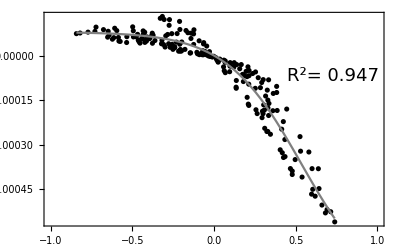

```mathematica
γDeivEMPlot=Module[{data},data=Transpose[{γDeivEM[[;;,1]]-γDeivEM[[;;,2]],γDeivEM[[;;,4]]}];
(*lmEM=LinearModelFit[data,x,x];*)
lmEM=NonlinearModelFit[data,y0+L/(1+Exp[-k(x-x0)]),{y0,L,k,x0},x];
Show[ListPlot[data,Frame->True,PlotStyle->Black],Plot[lmEM[x],{x,Min[data[[;;,1]]],Max[data[[;;,1]]]},PlotStyle->Gray],PlotRange->{{-1,1},Automatic},Epilog->Text[Style["R^2= "<>ToString[Round[lmEM["RSquared"],0.001]],18,Black],Scaled[{0.85,0.7}]],PlotOptions]
]
Export[NotebookDirectory[]<>"Plots/gammaDeivEM.pdf",γDeivEMPlot,ImageResolution->500];
```

## Individual Based Simulations (C++)

Making Input files

## Choosing Parameters

```mathematica
randPars[npts_(*,μIn_*)]:=Block[{out,ct,a,x,y,d,(*m,*)g},out={};
For[ct=1,ct≤npts,ct++,
d=RandomReal[{0.1,1}];a=RandomReal[{0,0.5}];x=RandomReal[];y=RandomReal[{0,x}];g=RandomReal[{0.1,1}];(*m=RandomInteger[{1,5}];*)
AppendTo[out,{X->x,Y->y,α->a,δ->d,γ->g(*,M->m,μ->μIn*)}];
];
out
]
```

```mathematica
pars1=randPars[100(*,0.001*)];
```

## Making Input File

```mathematica
file[pars_]:="input file for Moran MAM simulations

number of reps (nRep): 7
number of demes (nDemes): 1000
run time (tmax): 500
sampling frequency (sampFreq): 10
matching infection rate (X): "<>ToString[X/.pars]<>"
mismatching infection rate (Y): "<>ToString[Y/.pars]<>"
death probability (alpha): "<>ToString[α/.pars]<>"
host natural death rate (delta): "<>ToString[δ/.pars]<>"
pathogen natural death rate (gamma): "<>ToString[γ/.pars](*<>"
pathogen births per host (M): "<>ToString[M/.pars]<>"
pathogen mutation rate (mu): "<>ToString[μ/.pars]*);
```

```mathematica
exportFile[run_]:=Export["/Users/ailenemacpherson/Documents/VisualStudio/ConstantMAM/inputConst_"<>ToString[run]<>".txt",file[pars1[[run]]]]
```

```mathematica
Do[exportFile[run],{run,1,100}]
```

```mathematica
pars1[[1]]
```

{X→0.38676,Y→0.137576,α→0.381074,δ→0.991,γ→0.23825}

Importing Data

### Importing Data

File paths to simulation files.

```mathematica
(*file=NotebookDirectory[]<>"Sims/Moran/runConst_"; (*50 parameter sets*)*)
file2=NotebookDirectory[]<>"Sims/Moran_10_15/runConst_"; (*100 parameter sets*)
```

```mathematica
(*file="/Users/ailene/Documents/UBC/Warwick/ConstantSize/Sims/Moran/runConst_"; (*50 parameter sets*)*)
file2="/Users/ailene/Documents/UBC/Warwick/ConstantSize/Sims/Moran_10_15/runConst_"; (*100 parameter sets*)
```

```mathematica
Clear[pars]
pars[file_,run_]:=pars[file,run]=Import[file<>ToString[run]<>"/out.csv"]
```

```mathematica
Clear[nDemes,nRep,tmax,δ,X,Y,α,κ,γ]
nRep[file_,run_]:=pars[file,run][[2,2]]
nDemes[file_,run_]:=pars[file,run][[3,2]]
tmax[file_,run_]:=pars[file,run][[4,2]]
sampFreq[file_,run_]:=pars[file,run][[5,2]]
X[file_,run_]:=pars[file,run][[6,2]]
Y[file_,run_]:=pars[file,run][[7,2]]
α[file_,run_]:=pars[file,run][[8,2]]
δ[file_,run_]:=pars[file,run][[9,2]]
γ[file_,run_]:=pars[file,run][[10,2]]
(*M[file_,run_]:=pars[file,run][[11,2]]
μ[file_,run_]:=pars[file,run][[12,2]]*)
κ[file_,run_,rep_]:=pars[file,run][[12+rep,2]];
```

simPars[file,run,rep] gives a substitution list of the simulation parameters for simulations in the folder “file”, for parameter condition specified by “run” (run ranges between 1 and 100)., and growth limit κ specified by rep (rep ranges between 0 and 6).

```mathematica
simPars[file_,run_,rep_]:={X->X[file,run],Y->Y[file,run],α->α[file,run],δ->δ[file,run],γ->γ[file,run],(*M->M[file,run],*)κ->κ[file,run,rep]};
```

While no-longer strictly necessary fileExist is a useful troubleshooting tool that allows us to exclude cases where the simulation file doesn’t exist.

```mathematica
fileExist[file_,run_,rep_,t_]:=FileExistsQ[file<>ToString[run]<>"/rep_"<>ToString[rep]<>"/state_"<>ToString[t]<>".csv"]
```

repData is a {1000,8} matrix.  each row specifies a deme.  Columns 1 through 4 given the number of hosts of type 1, number of hosts of type 2, number of pathogens of type 1, and number of pathogens of 2 under host-parasite coevolution. Columns 5-8 are the analogous values under neutral genetic drift.

```mathematica
Clear[repData]
repData[file_,run_,rep_,t_]:=repData[file,run,rep,t]=Block[{name},
name=file<>ToString[run]<>"/rep_"<>ToString[rep]<>"/state_"<>ToString[t]<>".csv";
If[FileExistsQ[name]==True,Import[name]]
]
```

### Processing

For a given parameter condition (run and rep) the following three functions determine in which demes coevolution is ongoing (CoevSel), in which directional selection occurs (DirSel), and in which the host is fixed (fixed).

```mathematica
Clear[CoevSel]
CoevSel[file_,run_,rep_,t_]:=CoevSel[file,run,rep,t]=If[fileExist[file,run,rep,t],Quiet[Flatten[Position[repData[file,run,rep,t],_?((#[[1]]>0&&#[[2]]>0)&&(#[[3]]>0&&#[[4]]>0)&)]]]]
```

```mathematica
Clear[DirSel]
DirSel[file_,run_,rep_,t_]:=DirSel[file,run,rep,t]=If[fileExist[file,run,rep,t],Quiet[Flatten[Position[repData[file,run,rep,t],_?((#[[1]]>0&&#[[2]]>0)&&Xor[#[[3]]>0,#[[4]]>0]&)]]]]
```

```mathematica
Clear[fixed]
fixed[file_,run_,rep_,t_]:=fixed[file,run,rep,t]=If[fileExist[file,run,rep,t],Quiet[Flatten[Position[repData[file,run,rep,t],_?(Xor[#[[1]]>0.,#[[2]]>0.]&)]]]]
```

### Functions

#### Equilibrium

```mathematica
Clear[Dequ]
Dequ[file_,run_,rep_]:=(Sum[β[h,p]α (κ/2)^2,{h,1,2},{p,1,2}]+δ κ)/κ/.βSub/.simPars[file,run](*/.{κ-> 2+rep 0.25}*)
```

#### Bootstrap Functions

Takes nBoot bootstrap samples of data and calculates the mean of each.

```mathematica
BootstrapMean[data_,nBoot_]:=BootstrapMean[data,nBoot]=Block[{out,b},out={};
For[b=1,b≤nBoot,b++,
AppendTo[out,Mean[RandomChoice[data,Length[data]]]]
];
out]
```

Returns a bootstrap sample of data indexed by a dummy variable.

```mathematica
Bootstrap[data_,dummy_]:=Bootstrap[data,dummy]=RandomChoice[data,Length[data]]
```

#### Allele Frequency

Host allele frequency under coevolution

```mathematica
Clear[pH]
pH[file_,run_,rep_,t_]:=pH[file,run,rep,t]=If[fileExist[file,run,rep,t],(repData[file,run,rep,t][[;;,1]])/Total[Transpose[repData[file,run,rep,t][[;;,{1,2}]]]]//N]
```

Host allele frequency under neutral drift

```mathematica
Clear[pHn]
pHn[file_,run_,rep_,t_]:=pHn[file,run,rep,t]=If[fileExist[file,run,rep,t],(repData[file,run,rep,t][[;;,5]])/Total[Transpose[repData[file,run,rep,t][[;;,{5,6}]]]]//N]
```

Pathogen allele frequency under coevolution

```mathematica
Clear[pP]
pP[file_,run_,rep_,t_]:=pP[file,run,rep,t]=If[fileExist[file,run,rep,t],(repData[file,run,rep,t][[;;,3]])/Total[Transpose[repData[file,run,rep,t][[;;,{3,4}]]]]//N ]
```

#### Heterozygosity

Genetic variation (measured as heterozygosity) at time t simulated under coevolutionary selection.

```mathematica
Clear[GVar]
GVar[file_,run_,rep_,t_]:=GVar[file,run,rep,t]=If[fileExist[file,run,rep,t],2pH[file,run,rep,t](1-pH[file,run,rep,t])]
```

Genetic variation (measured as heterozygosity) at time t simulated under neutral genetic drift

```mathematica
Clear[GVarn]
GVarn[file_,run_,rep_,t_]:=GVarn[file,run,rep,t]=If[fileExist[file,run,rep,t],2pHn[file,run,rep,t](1-pHn[file,run,rep,t])]
```

Analytical expectation of genetic variation (measured as heterozygosity) at time t.

```mathematica
Clear[GVarn2]
GVarn2[file_,run_,rep_,t_]:=GVarn2[file,run,rep,t]=neutExp[κ/.simPars[file,run,rep],t]//N
```

```mathematica
Clear[ΔHet]
ΔHet[file_,run_,rep_,t_]:=If[fileExist[file,run,rep,t],Mean[GVar[file,run,rep,t]]-GVarn2[file,run,rep,t](*Mean[GVarn[file,run,rep,t]]*)]
```

Plotting

## EM dynamics

The Ensemble Moment dynamics for each parameter condition in the simulations

```mathematica
dynPlotEM[file_,tMax_]:=Block[{Δt,tList,rep},rep=1;Δt=sampFreq[file,1];tList=Join[Table[t,{t,0(*10*),tMax,Δt}]];
Show[
(*Ensemble Moment Dynamics*)
Table[Plot[nHet[simPars[file,run,rep],tMax,τ],{τ,0,tMax},PlotStyle->Directive[Darker[Green],Opacity[0.2]],Axes->False],{run,1,100}],
(*Analytical neutral expectation*)
Plot[neutExp[κ[file,1,rep],t],{t,0,tMax},PlotStyle->Directive[Thick,Blue]],
(*ListLinePlot[Table[{t,neutExp[κ[file,1,rep],t]},{t,tList}],PlotRange->{0,0.5},PlotStyle->Directive[Thick,Blue]],*)
(*Plot Options*)
PlotRange->{{0,tMax},{Automatic,0.5}}]]
```

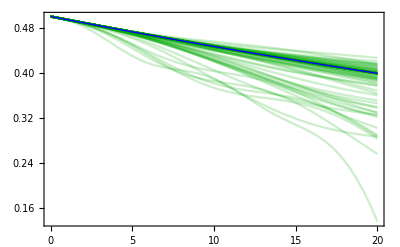

```mathematica
Show[dynPlotEM[file2,20],PlotOptions]
Export[NotebookDirectory[]<>"Plots/EmDyn.pdf",%];
```

### Deviation dynamics

```mathematica
Clear[temp,nlf]
```

```mathematica
temp[file_,run_,rep_]:=Table[{τ,nHet[simPars[file,run,rep],20,τ]-neutExp[κ[file,run,rep],τ]},{τ,0,20,0.05}]
```

```mathematica
tempPlot[run_]:=ListPlot[DeleteCases[{Map[{#[[1]],Log[Abs[#[[2]]]]}&,Select[temp[file2,run,3],#[[2]]<0&]],Map[{#[[1]],Log[Abs[#[[2]]]]}&,Select[temp[file2,run,3],#[[2]]>0&]]},{}],Joined->True]
```

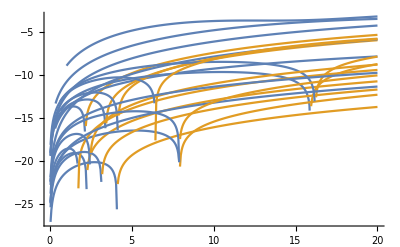

```mathematica
Show[Table[tempPlot[run],{run,1,20}],PlotRange->All]
```

```mathematica
Clear[nlf]
nlf[file_,run_,rep_]:=nlf[file,run,rep]=NonlinearModelFit[temp[file,run,rep],a Exp[b x],{a,b},{x}]
```

```mathematica
nlf[file2,1,3]
```

FittedModel[0.0000900168 ⅇ^(0.201065 x)]

```mathematica
expFit[file_,run_,rep_]:=Block[{},
nlf[file,run,rep];
Show[ListLinePlot[temp[file,run,rep],PlotStyle->Red],Plot[nlf[file,run,rep][x],{x,0,30},PlotStyle->Black],PlotOptions]]
```

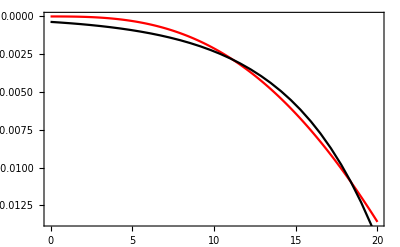

```mathematica
expFit[file2,5,3]
```

## Genetic Variation

### Dynamics

Plot of the dynamics for a given parameter condition (specified by file,run, and rep) up to time tMax.  Note that you have to run the Ensemble moment dynamics to calculate nHet, the dynamics of heterozygosity expected under that approximation.

```mathematica
dynPlot[file_,run_,rep_,tMax_]:=Block[{Δt,tList},Δt=sampFreq[file,run];tList=Join[Table[t,{t,0(*10*),tMax,Δt}]];
Show[
(*Coevolutionary heterozygosity*)
ListLinePlot[{Table[{t,Mean[GVar[file,run,rep,t]]},{t,tList}],Table[{t,Mean[GVar[file,run,rep,t]]+2 StandardDeviation[GVar[file,run,rep,t]]/Sqrt[Length[GVar[file,run,rep,t]]]},{t,tList}],Table[{t,Mean[GVar[file,run,rep,t]]-2 StandardDeviation[GVar[file,run,rep,t]]/Sqrt[Length[GVar[file,run,rep,t]]]},{t,tList}]},Filling->2->{3},PlotStyle->{Red,Pink,Pink},PlotRange->{0,0.5}],
(*Neutral heterozygosity from simulations*)ListLinePlot[{Table[{t,Mean[GVarn[file,run,rep,t]]},{t,tList}],Table[{t,Mean[GVarn[file,run,rep,t]]+2 StandardDeviation[GVarn[file,run,rep,t]]/Sqrt[Length[GVarn[file,run,rep,t]]]},{t,tList}],Table[{t,Mean[GVarn[file,run,rep,t]]-2 StandardDeviation[GVarn[file,run,rep,t]]/Sqrt[Length[GVarn[file,run,rep,t]]]},{t,tList}]},Filling->2->{3},PlotStyle->{Directive[Thick,Black],Gray,Gray},PlotRange->{0,0.5}],
(*Analytical neutral expectation*)
ListLinePlot[Table[{t,neutExp[κ[file,run,rep],t]},{t,tList}],PlotRange->{0,0.5},PlotStyle->Directive[Thick,Blue]],
(*Ensemble Moment Dynamics*)
Plot[nHet[simPars[file,run,rep],100,τ],{τ,0,100},PlotStyle->Directive[{Thickness[0.008],Darker[Green]}]],PlotRange->{{0,tMax},{Floor[neutExp[κ[file,run,rep],tMax],0.1],0.5}},Frame->True,FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5},False},{True,False}},ImageSize->{400,Automatic}(*,Epilog->Inset[barplot[run,rep,tMax,2],Scaled[{0.49,0.12}]]*)]]
```

Zoomed in

```mathematica
simPars[file2,1,3]
```

{X→0.38676,Y→0.137576,α→0.381074,δ→0.991,γ→0.23825,κ→562.341}

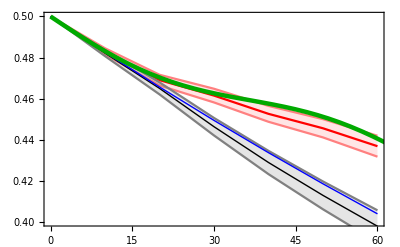

```mathematica
Show[dynPlot[file2,1,3,60],PlotOptions]
(*Export[NotebookDirectory[]<>"Plots/EgDynSub.pdf",%];*)
```

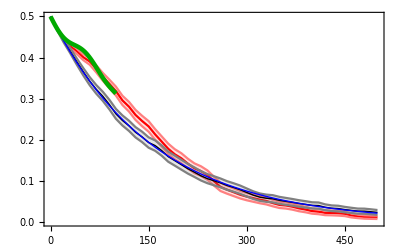

```mathematica
Show[dynPlot[file2,1,2,500],PlotOptions]
Export[NotebookDirectory[]<>"Plots/EgDynFull_2.pdf",%];
```

```mathematica
lineLeg2=LineLegend[{{Blue,Thick},{Black,Thick},{Darker[Green],Thick},Directive[Red]},{"analytical H_neut","simulated H_neut","EM approximation","mean H_coev"},LegendFunction->"Frame",LabelStyle->Directive[Bold, 14]]
Export[NotebookDirectory[]<>"Plots/lineLeg2.pdf",%];
```

```mathematica
dynPlot2[file_,run_,rep_,tMax_]:=Block[{Δt,tList},Δt=sampFreq[file,run];tList=Join[Table[t,{t,0(*10*),tMax,Δt}]];
Show[
(*Analytical neutral expectation*)
ListLinePlot[Table[{t,neutExp[κ[file,run,rep],t]},{t,tList}],PlotRange->{0,0.5},PlotStyle->Directive[Thick,Blue]],
(*Ensemble Moment Dynamics*)
Plot[nHet[simPars[file,run,rep],tMax,τ],{τ,0,tMax},PlotStyle->Directive[{Thickness[0.008],Darker[Green]}]],PlotRange->{{0,tMax},{Floor[neutExp[κ[file,run,rep],tMax],0.1],0.5}},Frame->True,FrameTicks->{{{0,0.1,0.2,0.3,0.4,0.5},False},{True,False}},ImageSize->{400,Automatic}(*,Epilog->Inset[barplot[run,rep,tMax,2],Scaled[{0.49,0.12}]]*),ImageSize->{Automatic,300},Frame->True,FrameTicksStyle->Directive[Black,Bold,14],FrameTicks->{{True,False},{True,False}},Background->White]]
```

```mathematica
EMDynPlot[file_,run_,rep_]:=Plot[nHet[simPars[file,run,rep],30,τ],{τ,0,50},PlotStyle->Directive[{Thick,Blue,Opacity[0.3]}]]
```

Does heterozygosity decline exponentially?

```mathematica
temp=Table[{τ,Mean[Table[Mean[GVar[file2,run,2,τ]],{run,1,100}]]},{τ,0,500,10}];
```

```mathematica
lm=NonlinearModelFit[temp, 0.5Exp[-b x],{b},{x}]
```

FittedModel[0.5 ⅇ^(-0.00828892 x)]

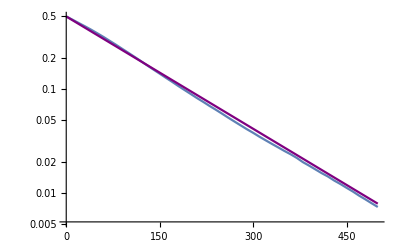

```mathematica
Show[ListLogPlot[temp,Joined->True],LogPlot[lm[x],{x,0,500},PlotStyle->Purple]]
```

Heterozygosity across parameter combinations

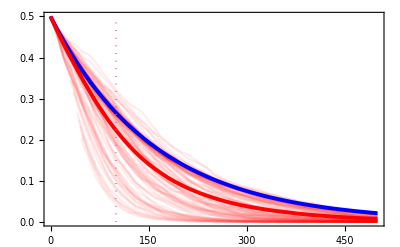

```mathematica
GMeanDynPlot[file_,run_,rep_]:=ListLinePlot[Table[{τ,Mean[GVar[file,run,rep,τ]]},{τ,0,500,10}],PlotStyle->Directive[{Red,Opacity[0.07]}]];
GMeanMeanDynPlot[file_,rep_]:=ListLinePlot[Table[{τ,Mean[Table[Mean[GVar[file,run,rep,τ]],{run,1,100}]]},{τ,0,500,10}],PlotStyle->Directive[Red,Thickness[0.007]]];
Show[Join[
(*All Means*)
Table[GMeanDynPlot[file2,run,2],{run,1,100}],
(*Neutral expectation*)
{Plot[neutExp[κ[file2,1,2],τ],{τ,0,500},PlotStyle->Directive[Thickness[0.007],Blue]]},
(*Example Line*)
(*{ListLinePlot[Table[{τ,Mean[GVar[file2,1,2,τ]]},{τ,0,500,10}],PlotStyle->Directive[{Thick,Red}]]},*)
{GMeanMeanDynPlot[file2,2]},
(*Vertical Line*)
{ListLinePlot[{{100,0},{100,0.5}},PlotStyle->Directive[Dotted,ColorData["CMYKColors"][2/6]]]}],PlotRange->{0,0.5},Axes->None,PlotOptions]
Export[NotebookDirectory[]<>"Plots/meanDyn_2.pdf",%,ImageResolution->300];
```

```mathematica
lineLeg3=LineLegend[{Directive[Blue,Thickness[0.007]],Directive[Red,Thickness[0.007]](*,Directive[Dashed,ColorData["CMYKColors"][2/6]]*)},{"analytical H_neut","mean H_coev"(*,"panel A"*)},LegendFunction->"Frame",LabelStyle->Directive[Bold, 14]]
Export[NotebookDirectory[]<>"Plots/lineLeg3.pdf",%];
```

### ΔH Distribution

An alternative way of exploring the effect of coevolution on host heterozygosity by focusing on the distributions in ΔH, the change in heterozygosity between the coevolutionary and neutral simulations.

```mathematica
ΔHList[file_,rep_,t_]:=Select[Table[ΔHet[file,run,rep,t],{run,1,60}],#≠"Null"&]
```

```mathematica
HetBW[file_,nReps_,t_]:=Block[{sigData,rep,temp,point},sigData={};
point=Graphics[{EdgeForm[Black],White,Disk[Scaled[{0.5,0.5}],0.02]}];
(*Which reps are signifcantly DIFFERENT From 0*)
For[rep=0,rep≤nReps,rep++,
If[Mean[BootstrapMean[ΔHList[file,rep,t],1000]]+1.6 StandardDeviation[BootstrapMean[ΔHList[file,rep,t],1000]]<0 (*||Mean[BootstrapMean[ΔHList[file,rep,t],10000]]-2 StandardDeviation[BootstrapMean[ΔHList[file,rep,t],10000]]>0*),
AppendTo[sigData,{{rep+1,0.13}}],If[Mean[BootstrapMean[ΔHList[file,rep,t],1000]]-1.6 StandardDeviation[BootstrapMean[ΔHList[file,rep,t],1000]]>0,AppendTo[sigData,{{rep+1,-0.45}}],AppendTo[sigData,{{rep+1,-0.6}}]]]
];
Show[
(*Adds stars for all distributions where the mean differs significantly from 0*)
ListPlot[sigData,PlotStyle->Table[ColorData["CMYKColors"][rep/nReps],{rep,0,nReps}],PlotMarkers->✶],
(*Violins*)
DistributionChart[Table[ΔHList[file,rep,t],{rep,0,nReps}],ChartStyle->Table[ColorData["CMYKColors"][rep/nReps],{rep,0,nReps}]],
(*Neutral line*)
ListLinePlot[{{0.2,0},{8,0}},PlotStyle->Directive[Black]],
(*Data points*)ListPlot[Table[Transpose[{RandomReal[{1+rep-0.1,1+rep+0.1},Length[ΔHList[file,rep,t]]],ΔHList[file,rep,t]}],{rep,0,6}],PlotMarkers->point],
(*Plot Options*)
PlotRange->{-0.35,Automatic},AxesOrigin->{Automatic,-0.5},Frame->True,FrameLabel->{"Log_10[κ]","ΔH"},FrameTicks->{{True,False},{Table[{rep+1,2+rep*0.25},{rep,0,nReps}],False}},LabelStyle->Directive[Black,Bold, 18],FrameTicksStyle->Directive[14],ImageSize->Large]
]
```

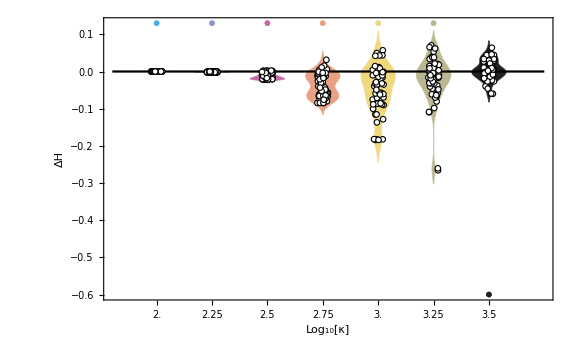

```mathematica
HetBW[file,6,500]
Export[NotebookDirectory[]<>"Plots/Moran_HetBW.gif",%,ImageResolution->300];
```

### Mean Heterozygosity vs. Neutral Expectation

#### LOESS Smoothing

Project data onto the X=Y line.

```mathematica
Clear[dataNew]
dataNew[data_]:=dataNew[data]=Transpose[{Cos[Abs[ArcTan[data[[;;,2]]/data[[;;,1]]]-π/4]]*Sqrt[Total[Transpose[data^2]]],Sin[ArcTan[data[[;;,2]]/data[[;;,1]]]-π/4]*Sqrt[Total[Transpose[data^2]]]}]
```

A gaussian weighting of the data  near the point xNew along the X=Y line

```mathematica
Clear[weights]
weights[xNew_,αW_,data_]:=weights[xNew,αW,data]=Exp[-(dataNew[data][[;;,1]]-xNew)^2/(2 αW^2)];
```

Find the weighted mean and standard deviation and standard error.

```mathematica
Clear[meanNew]
meanNew[xNew_,αW_,data_]:=meanNew[xNew,αW,data]=Total[weights[xNew,αW,data]dataNew[data][[;;,2]]]/Total[weights[xNew,αW,data]]
```

```mathematica
SDNew[xNew_,αW_,data_]:=Sqrt[Total[weights[xNew,αW,data]*(dataNew[data][[;;,2]]-meanNew[xNew,αW,data])^2]/Total[weights[xNew,αW,data]]]
```

```mathematica
SENew[xNew_,αW_,data_]:=SDNew[xNew,αW,data]/Sqrt[Total[weights[xNew,αW,data]]]
```

The rolling average fit along the X+Y line (rotated plot)

```mathematica
Clear[RollFit]
RollFit[αW_,npts_,data_]:=RollFit[αW,npts,data]=Table[{x,meanNew[x,αW,data]},{x,0.001(*Sqrt[2*0.5^2]/(npts+2)*),Sqrt[2*0.5^2](*-Sqrt[2*0.5^2]/(npts+2)*),(Sqrt[2*0.5^2]-0.001)/(npts+2)}];
```

Projecting back into the original coordinates.

```mathematica
RollFitOld[αW_,npts_,data_]:=Transpose[{Cos[ArcTan[(RollFit[αW,npts,data][[;;,2]])/(RollFit[αW,npts,data][[;;,1]])]+π/4]Sqrt[(RollFit[αW,npts,data][[;;,2]])^2+(RollFit[αW,npts,data][[;;,1]])^2],Sin[ArcTan[(RollFit[αW,npts,data][[;;,2]])/(RollFit[αW,npts,data][[;;,1]])]+π/4]Sqrt[(RollFit[αW,npts,data][[;;,2]])^2+(RollFit[αW,npts,data][[;;,1]])^2]}]
```

#### Plotting

```mathematica
GVarList[file_,t_]:=Block[{run,rep,out},out={};
For[rep=0,rep≤6,rep++,
AppendTo[out,{}];
For[run=1,run≤100,run++,
If[fileExist[file,run,rep,t],AppendTo[out[[-1]],{GVarn2[file,run,rep,t](*Mean[GVarn[file,run,rep,t]]*),Mean[GVar[file,run,rep,t]]}]]
]
];
out
]
```

Identifying which data points differ significantly from the neutral expectation (given the Bonferroni correction).

```mathematica
ΔHrep[file_,run_,rep_,t_]:=GVar[file,run,rep,t]-GVarn[file,run,rep,t]
Clear[sigΔH]
sigΔH[file_,t_]:=sigΔH[file,t]=Block[{outSig,outNotSig,run,rep,CIU,CIL},outSig={};outNotSig={};
For[rep=0,rep≤6,rep++,
AppendTo[outSig,{}];AppendTo[outNotSig,{}];
For[run=1,run≤100,run++,
If[fileExist[file,run,rep,t],
CIU=Mean[ΔHrep[file,run,rep,t]]+(*1.96*)2.64 StandardDeviation[BootstrapMean[ΔHrep[file,run,rep,t],1000]];
CIL=Mean[ΔHrep[file,run,rep,t]]-(*1.96*)2.64 StandardDeviation[BootstrapMean[ΔHrep[file,run,rep,t],1000]];
If[CIU>0&&CIL<0,AppendTo[outNotSig[[-1]],{(*GVarn2[file,run,rep,t]*)Mean[GVarn[file,run,rep,t]],Mean[GVar[file,run,rep,t]]}],AppendTo[outSig[[-1]],{(*GVarn2[file,run,rep,t]*)Mean[GVarn[file,run,rep,t]],Mean[GVar[file,run,rep,t]]}]]]
]
];
{outNotSig,outSig}
]
```

Printing out mean fit for comparison to WF model. Exports only points less than the largest observed heterozygosity- prevents extrapolation.

```mathematica
Module[{temp,t},
For[t=50,t≤500,t+=50,
temp=Select[RollFitOld[0.1,40,Flatten[GVarList[file2,t],1]],#[[2]]<GVarList[file2,t][[-1,1,1]]&&#[[2]]>GVarList[file2,t][[1,1,1]]&];
Export[NotebookDirectory[]<>"MoranMean_"<>ToString[t]<>".csv",temp];(*Print[t];*)
]
]
```

```mathematica
moranMean[t_]:=Import[NotebookDirectory[]<>"MoranMean_"<>ToString[t]<>".csv"];
```

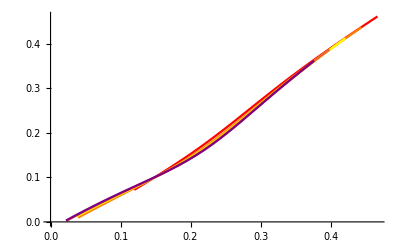

```mathematica
ListLinePlot[Table[moranMean[t],{t,100,500,100}],PlotStyle->{Red,Orange, Yellow, Green Blue,Purple, Pink,Black}]
```

Percent of data points that did not differ significantly from the neutral expectation.

```mathematica
PercentNeut[file_,rep_,t_]:=Length[sigΔH[file,t][[1,rep+1]]]
```

Figure 4A in the main text.

```mathematica
MeanFit[file_,t_]:=Show[
(*Bootstrap samples*)
ListLinePlot[Table[RollFitOld[0.1,40,Bootstrap[Flatten[GVarList[file,t],1],x]],{x,1,1000}],PlotStyle->Directive[Pink,Opacity[0.02]]],Plot[x,{x,0,0.5},PlotStyle->Directive[Black,Dashed]],
(*Mean*)
ListLinePlot[RollFitOld[0.1,40,Flatten[GVarList[file,t],1]],PlotStyle->Red],
(*Pointss*)
ListPlot[Select[sigΔH[file,t][[1]],#≠{}&],PlotStyle->Table[Lighter[ColorData["CMYKColors"][rep/6]],{rep,0,6}],PlotMarkers->○],ListPlot[Select[sigΔH[file,t][[2]],#≠{}&],PlotStyle->Table[Directive[ColorData["CMYKColors"][rep/6]],{rep,0,6}],PlotMarkers->●],AspectRatio->1,PlotRange->{{0,0.5},{0,0.5}},PlotOptions]
```

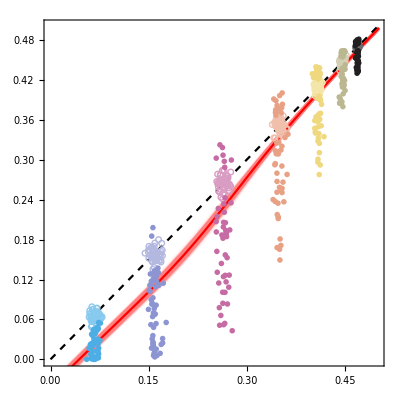

```mathematica
MeanFit[file2,100]
Export[NotebookDirectory[]<>"Plots/IBS_100.pdf",%,ImageResolution->300];
```

```mathematica
κLeg=PointLegend[Table[ColorData["CMYKColors"][rep/6],{rep,0,6}],Table[ToString[Round[10^(2+0.25rep)]]<>" ("<>ToString[PercentNeut[file2,rep,100]]<>"%)",{rep,0,6}],LegendFunction->"Frame",LegendLabel->Text[Style["κ",14,Bold]],LegendMarkerSize->15]
Export[NotebookDirectory[]<>"Plots/kappaLeg.pdf",κLeg];
```

```mathematica
lineLeg1=LineLegend[{{Black,Dashed},Red,{Pink,Opacity[0.5]}},{"neutral Expectation","mean H_coev","bootstrap means"},LegendFunction->"Frame",LabelStyle->Directive[Bold, 16]]
Export[NotebookDirectory[]<>"Plots/lineLeg1.pdf",%];
```

#### Percent of points Above, Not Significantly different from, and below neutral

```mathematica
ΔHrep[file_,run_,rep_,t_]:=GVar[file,run,rep,t]-GVarn[file,run,rep,t]
Clear[sigRun]
sigRun[file_,t_]:=sigRun[file,t]=
Block[{outG,outL,outNotSig,run,rep,CIU,CIL},
outG={};outL={};outNotSig={};
For[rep=0,rep≤6,rep++,
For[run=1,run≤100,run++,
If[fileExist[file,run,rep,t],
(*Calculaate confidence intervals*)
CIU=Mean[ΔHrep[file,run,rep,t]]+(*1.96*)2.64 StandardDeviation[BootstrapMean[ΔHrep[file,run,rep,t],1000]];
CIL=Mean[ΔHrep[file,run,rep,t]]-(*1.96*)2.64 StandardDeviation[BootstrapMean[ΔHrep[file,run,rep,t],1000]];
(*ΔH=0*)
If[CIU>0&&CIL<0,AppendTo[outNotSig,{run,rep}],
(*ΔH>0*)
If[CIU>0&&CIL>0,AppendTo[outG,{run,rep}],
(*ΔH<0*)
AppendTo[outL,{run,rep}]]]]
]
];
{outG,outNotSig,outL}
]
```

```mathematica
(sigRun[file2,100][[1]]//Length)/700//N
```

0.1

```mathematica
(sigRun[file2,100][[2]]//Length)/700//N
```

0.521429

```mathematica
(sigRun[file2,100][[3]]//Length)/700//N
```

0.378571

### Effect of relative turnover

Although not presented in the main text we can observe the effect of perturbations on the deviation from the neutral expectation as expected from the ensemble moment approximation.

```mathematica
Clear[ΔHγList]
```

```mathematica
ΔHγList[file_,rep_,t_]:=Select[Table[{γ[file,run]/Dequ[file,run,rep],ΔH[file,run,rep,t]},{run,1,60}] ,#[[2]]≠"Null"&]
```

```mathematica
γPlot[file_,rep_,t_]:=Block[{data,lm},
data=Select[ΔHγList[file,rep,t],(*#[[2]]<0&&*)#[[1]]<9&];
lm=LinearModelFit[data,x,x];
(*lm=NonlinearModelFit[data,a Exp[b x],{a,b},x];*)
R2[rep]=lm["RSquared"];
Show[ListPlot[data,PlotStyle->ColorData["CMYKColors"][rep/6],Frame->True,(*FrameLabel->{"γ/D: Rate of Pathogen Deaths","ΔH"},*)ImageSize->Large],Plot[lm[x],{x,Min[data[[;;,1]]],Max[data[[;;,1]]]},PlotStyle->ColorData["CMYKColors"][rep/6]],PlotRange->All]
]
```

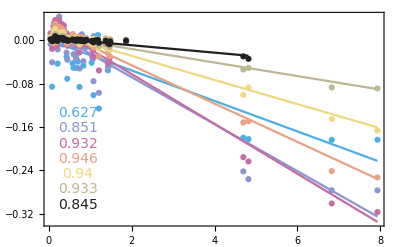

```mathematica
Show[Table[γPlot[file,rep,50],{rep,0,6}],Epilog->Table[Text[Style[(*"R^2="<>*)ToString[Round[R2[rep],0.001]],14,ColorData["CMYKColors"][rep/6]],Scaled[{0.1,0.1+(0.6-0.1)/7(6-rep)}]],{rep,0,6}],FrameTicksStyle->Directive[Black,Bold,14],ImageSize->{Automatic,300}(*,LabelStyle->Directive[Black,Bold, 18],FrameLabel->{"γ/D̂",ΔH}*)]
Export[NotebookDirectory[]<>"Plots/gammaDeivIBS.pdf",%,ImageResolution->300];
```

#### γ-δ above, below and at the neutral expectation

```mathematica
sigRun[file2,100][[2]]//Length
```

364

```mathematica
γδG=Map[γ-δ/.simPars[file2,#[[1]],#[[2]]]&,sigRun[file2,100][[1]]];
```

```mathematica
Round[{Mean[γδG],StandardDeviation[γδG]},0.001]
```

{-0.455,0.178}

```mathematica
γδEq=Map[γ-δ/.simPars[file2,#[[1]],#[[2]]]&,sigRun[file2,100][[2]]];
```

```mathematica
Round[{Mean[γδEq],StandardDeviation[γδEq]},0.001]
```

{-0.116,0.269}

```mathematica
γδL=Map[γ-δ/.simPars[file2,#[[1]],#[[2]]]&,sigRun[file2,100][[3]]];
```

```mathematica
Round[{Mean[γδL],StandardDeviation[γδL]},0.001]
```

{0.344,0.268}

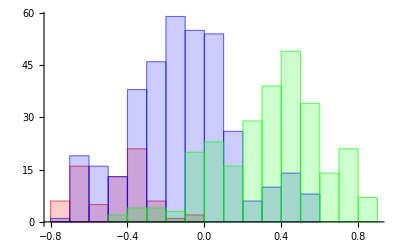

```mathematica
Histogram[{γδG,γδEq,γδL},ChartStyle->{Directive[Red,Opacity[0.2]],Directive[Blue,Opacity[0.2]],Directive[Green,Opacity[0.2]]}]
```

### Effect of leading eigenvalue

```mathematica
Clear[λIm]
λIm[file_,rep_]:=λIm[file,rep]=Table[{Mean[GVar[file,run,rep,100]]-Mean[GVarn[file,run,rep,100]],Log10[((X-Y) α)/((X+Y) α+2 δ)]}/.simPars[file,run,rep],{run,1,100}]
```

```mathematica
Clear[lm2]
lm2[file_,rep_]:=lm2[file,rep]=LinearModelFit[λIm[file,rep],x,x]
```

```mathematica
Table[LinearModelFit[λIm[file2,rep],x,x]["RSquared"],{rep,0,6}]//Mean
```

0.281519

```mathematica
leg=LineLegend[Table[ColorData["CMYKColors"][rep/6],{rep,0,6}],Table[Text[Style[ToString[LinearModelFit[λIm[file2,rep],x,x]["RSquared"]],ColorData["CMYKColors"][rep/6]]],{rep,0,6}],Background->White];
```

```mathematica
λPlot[file_]:=Block[{out,rep,CIL,CIU},out={};
For[rep=0,rep≤6,rep++,
{CIL,CIU}=lm2[file,rep]["ParameterConfidenceIntervals"][[2]];
If[Sign[CIL]==Sign[CIU],
AppendTo[out,Plot[lm2[file,rep][x],{x,-0.2,0.1},PlotStyle->Directive[ColorData["CMYKColors"][rep/6]]]]];
AppendTo[out,ListPlot[λIm[file,rep],PlotStyle->Directive[ColorData["CMYKColors"][rep/6]]]];
];
Show[out,PlotOptions]
]
```

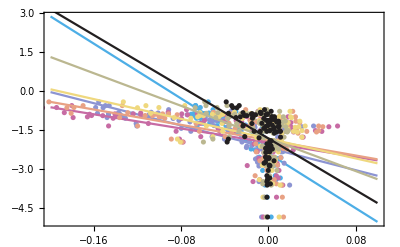

```mathematica
λPlot[file2]
```

```mathematica
λImG=Map[((X-Y) α)/((X+Y) α+2 δ)/.simPars[file2,#[[1]],#[[2]]]&,sigRun[file2,100][[1]]];
```

```mathematica
Round[{Mean[λImG],StandardDeviation[λImG]},0.001]
```

{0.051,0.035}

```mathematica
λImEq=Map[((X-Y) α)/((X+Y) α+2 δ)/.simPars[file2,#[[1]],#[[2]]]&,sigRun[file2,100][[2]]];
```

```mathematica
Round[{Mean[λImEq],StandardDeviation[λImEq]},0.001]
```

{0.025,0.038}

```mathematica
λImL=Map[((X-Y) α)/((X+Y) α+2 δ)/.simPars[file2,#[[1]],#[[2]]]&,sigRun[file2,100][[3]]];
```

```mathematica
Round[{Mean[λImL],StandardDeviation[λImL]},0.001]
```

{0.117,0.082}

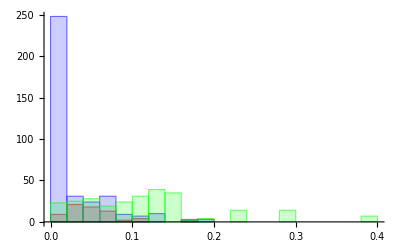

```mathematica
Histogram[{λImG,λImEq,λImL},ChartStyle->{Directive[Red,Opacity[0.2]],Directive[Blue,Opacity[0.2]],Directive[Green,Opacity[0.2]]}]
```

### Effect of X-Y/(X+Y)

```mathematica
Clear[CovSel]
CovSel[file_,rep_]:=CovSel[file,rep]=Table[{Mean[GVar[file,run,rep,100]]-Mean[GVarn[file,run,rep,100]],Log10[(X-Y)/(X+Y)]}/.simPars[file,run,rep],{run,1,100}]
```

```mathematica
Clear[lm3]
lm3[file_,rep_]:=lm3[file,rep]=LinearModelFit[CovSel[file,rep],x,x]
```

```mathematica
Table[LinearModelFit[CovSel[file2,rep],x,x]["RSquared"],{rep,0,6}]//Mean
```

0.106613

```mathematica
CovSelPlot[file_]:=Block[{out,rep,CIL,CIU},out={};
For[rep=0,rep≤6,rep++,
{CIL,CIU}=lm2[file,rep]["ParameterConfidenceIntervals"][[2]];
If[Sign[CIL]==Sign[CIU],
AppendTo[out,Plot[lm3[file,rep][x],{x,-0.2,0.1},PlotStyle->Directive[ColorData["CMYKColors"][rep/6]]]]];
AppendTo[out,ListPlot[CovSel[file,rep],PlotStyle->Directive[ColorData["CMYKColors"][rep/6]]]];
];
Show[out,PlotOptions]
]
```

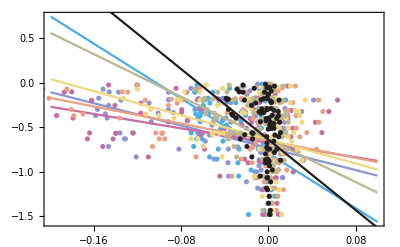

```mathematica
CovSelPlot[file2]
```

```mathematica
CovSelG=Map[(X-Y)/(X+Y)/.simPars[file2,#[[1]],#[[2]]]&,sigRun[file2,100][[1]]];
```

```mathematica
Round[{Mean[CovSelG],StandardDeviation[CovSelG]},0.001]
```

{0.38,0.207}

```mathematica
CovSelEq=Map[(X-Y)/(X+Y)/.simPars[file2,#[[1]],#[[2]]]&,sigRun[file2,100][[2]]];
```

```mathematica
Round[{Mean[CovSelEq],StandardDeviation[CovSelEq]},0.001]
```

{0.298,0.267}

```mathematica
CovSelL=Map[(X-Y)/(X+Y)/.simPars[file2,#[[1]],#[[2]]]&,sigRun[file2,100][[3]]];
```

```mathematica
Round[{Mean[CovSelL],StandardDeviation[CovSelL]},0.001]
```

{0.472,0.226}

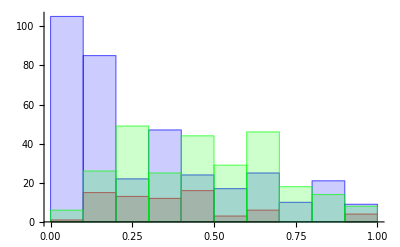

```mathematica
Histogram[{CovSelG,CovSelEq,CovSelL},ChartStyle->{Directive[Red,Opacity[0.2]],Directive[Blue,Opacity[0.2]],Directive[Green,Opacity[0.2]]}]
```

## Stochastic Phase Plane

```mathematica
Clear[traj2]
traj2[file_,run_,rep_,deme_]:=traj2[file,run,rep,deme]=Block[{outC,outD,outN,t},
outC={};outD={};outN={};
For[t=0,t≤500,t=t+sampFreq[file,run],
(*Print[{t,pH[run,rep,d,t],pP[run,rep,d,t]} ];*)
If[0<pH[file,run,rep,t][[deme]]<1,If[0<pP[file,run,rep,t][[deme]]<1,
(*Ongoing Coevolution*)AppendTo[outC,{(*t,*)pH[file,run,rep,t][[deme]],pP[file,run,rep,t][[deme]]}],
(*Monomorphic pathogen*)AppendTo[outD,{(*t,*)pH[file,run,rep,t][[deme]],pP[file,run,rep,t][[deme]]}]],
(*Fixed Host*)AppendTo[outN,{(*t,*)pH[file,run,rep,t][[deme]],pP[file,run,rep,t][[deme]]}]
]
];
If[Length[outD]>0,AppendTo[outC,outD[[1]]],If[Length[outN]>0,AppendTo[outC,outN[[1]]]]];
If[Length[outN]>0,AppendTo[outD,outN[[1]]]];
{outC,Select[outD,#≠{}&],Select[outN,#≠{}&]}//N
]
```

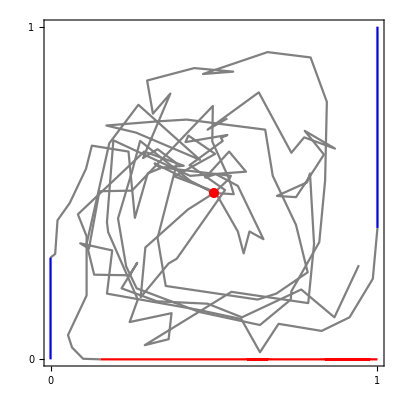

```mathematica
Show[ListLinePlot[Table[traj2[file2,4,3,d][[1]],{d,{1,2,3,4,5}}],PlotStyle->Gray],
ListLinePlot[DeleteCases[Table[traj2[file2,4,3,d][[2]],{d,{1,2,3,4,5}}],{}],PlotStyle->Red],
ListLinePlot[DeleteCases[Table[traj2[file2,4,3,d][[3]],{d,{1,2,3,4,5}}],{}],PlotStyle->Blue],ListPlot[{{0.5,0.5}},PlotMarkers->{Automatic, Medium},PlotStyle->Red],PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->{{{0,1},False},{{0,1},False}},AspectRatio->1]
```

```mathematica
phasePlane1[file_,run_,rep_,d_]:=Show[ListLinePlot[traj2[file,run,rep,d][[1]],PlotStyle->Gray,PlotRange->All],
ListLinePlot[traj2[file,run,rep,d][[2]],PlotStyle->Red,PlotRange->All],
ListLinePlot[traj2[file,run,rep,d][[3]],PlotStyle->Blue,PlotRange->All],ListPlot[{{0.5,0.5}},PlotMarkers->{Automatic, Medium},PlotStyle->Red],PlotRange->{{0,1},{0,1}},Frame->True,FrameTicks->False,AspectRatio->1,Axes->False,ImageSize->Small]
```

```mathematica
Do[Export[NotebookDirectory[]<>"Plots/StochasticPhasePlane_"<>ToString[d]<>".pdf",phasePlane1[file2,4,3,d],ImageResolution->300];,{d,1,8}]
```

```mathematica
phaseData[file_,run_,rep_,deme_]:=Table[{pH[file,run,rep,t][[deme]],pP[file,run,rep,t][[deme]]},{t,0,500,10}]
```

```mathematica
phaseDataMean[file_,run_,rep_]:=Table[{Mean[pH[file,run,rep,t]],Mean[pP[file,run,rep,t]]},{t,0,500,10}]
```

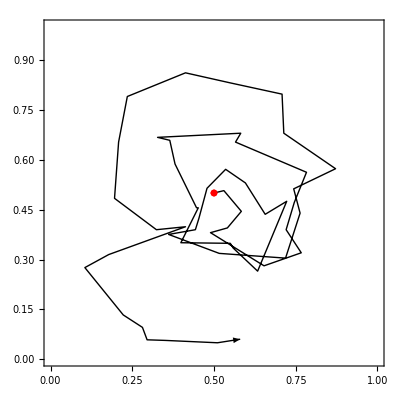

```mathematica
Show[Graphics[Arrow[phaseData[file2,1,3,1]],PlotOptions,PlotRange->{{0,1},{0,1}}],
ListPlot[{{0.5,0.5}},PlotStyle->Red,PlotMarkers->{Automatic, Small}]]
Export[NotebookDirectory[]<>"Plots/StochasticPhasePlane.pdf",%,ImageResolution->200];
```

## Allele Frequency Trajectories

```mathematica
Clear[traj]
traj[file_,run_,rep_,tLim_]:=traj[file,run,rep,tLim]=Block[{outC,outD,outN,t,d},outC={};outD={};outN={};
For[d=1,d<500(*nDemes[run]*),d++,
AppendTo[outC,{}];AppendTo[outD,{}];AppendTo[outN,{}];
For[t=0,t≤tLim,t=t+sampFreq[file,run],
(*Print[{t,pH[run,rep,d,t],pP[run,rep,d,t]} ];*)
If[0<pH[file,run,rep,t][[d]]<1,If[0<pP[file,run,rep,t][[d]]<1,
(*Ongoing Coevolution*)AppendTo[outC[[-1]],{t,pH[file,run,rep,t][[d]]}],
(*Monomorphic pathogen*)AppendTo[outD[[-1]],{t,pH[file,run,rep,t][[d]]}]],
(*Fixed Host*)AppendTo[outN[[-1]],{t,pH[file,run,rep,t][[d]]}]
]
]
];
{outC,Select[outD,#≠{}&],Select[outN,#≠{}&]}//N
]
```

```mathematica
AFDyn[file_,run_,rep_,tLim_]:=Show[{ListLinePlot[traj[file,run,rep,tLim][[1]],PlotRange->{0,1},PlotStyle->Directive[Gray,Opacity[0.1]]],ListLinePlot[traj[file,run,rep,tLim][[2]],PlotRange->{0,1},PlotStyle->Directive[Red,Opacity[0.2]]],ListLinePlot[traj[file,run,rep,tLim][[3]],PlotRange->{0,1},PlotStyle->Directive[Blue,Opacity[0.2]]]},PlotRange->{-0.05,1.05},PlotOptions]
```

Figure 4C in the main text.

```mathematica
simPars[file2,4,3]
```

{X→0.14741,Y→0.102564,α→0.341771,δ→0.207544,γ→0.214468,κ→562.341}

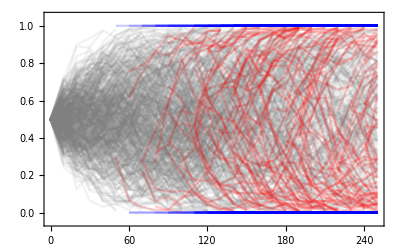

```mathematica
AFDyn[file2,4,3,250]
Export[NotebookDirectory[]<>"Plots/Moran_AF_Dyn.pdf",%,ImageResolution->300];
```

```mathematica
simPars[file2,4,3]
```

{X→0.14741,Y→0.102564,α→0.341771,δ→0.207544,γ→0.214468,κ→562.341}

```mathematica
LineLegend[{Gray,Red,Blue},{"coevolution","directional selection","fixed"},Background->White]
Export[NotebookDirectory[]<>"Plots/AFDynLeg.pdf",%,ImageResolution->200];
```

## Proportion of Lineages

```mathematica
outcome[file_,run_,rep_,t_]:=Block[{temp},
temp=Transpose[{pH[file,run,rep,t],pP[file,run,rep,t]}];
{Length[Select[temp,(#[[1]]≠0&&#[[1]]≠1)&&(#[[2]]≠0&&#[[2]]≠1)&]],Length[Select[temp,(#[[1]]≠0&&#[[1]]≠1)&&(#[[2]]==0||#[[2]]==1)&]],Length[Select[temp,(#[[1]]==0||#[[1]]==1)&]]}]
```

```mathematica
outcomeList[file_,rep_,t_]:=Sort[Table[{Mean[ΔHrep[file,run,rep,t]],outcome[file,run,rep,t]},{run,1,100}],#1[[1]]>#2[[1]]&][[;;,2]]
```

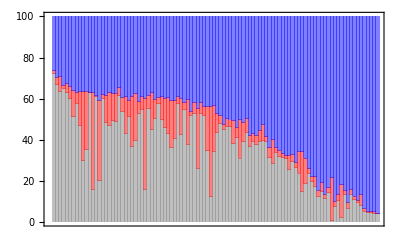

```mathematica
BarChart[outcomeList[file2,3,250]/10,ChartLayout->"Stacked",ChartStyle->{Directive[Gray,Opacity[0.5]],Directive[Red,Opacity[0.5]],Directive[Blue,Opacity[0.5]]},FrameTicks->{{True,False},{False,False}},PlotOptions,PlotRange->{{0,100},{0,100}}]
Export[NotebookDirectory[]<>"Plots/Moran_outcome.pdf",%,ImageResolution->300];
```

```mathematica
SwatchLegend[{Gray,Red,Blue},{"Coevolution","Directional Selection","Fixed"},Background->White]
Export[NotebookDirectory[]<>"Plots/outcomeLeg.pdf",%,ImageResolution->200];
```